Fisher Information
From Apr. 29th, 2022 to Jul. 13th, 2022
Non-Gaussian Team
Professor: Christos Gagatsos
Author: Sijie Cheng
Acknowledge:
	Hongji Wei (Physics in UofA)
	Andrew Pizzimenti (Optical Science in UofA)

# PART I Simplify “NGFI.nb”

```mathematica
Wnr=  (ⅇ^(-r^2))/π(-1)^n LaguerreL[n,2 r^2]
JWnr = Simplify[2π*r/Wnr*(D[Wnr,r])^2]
JWnr=JWnr/(4r)/.{r->Sqrt[x/2]}
```

((-1)^n ⅇ^(-r^2) LaguerreL[n,2 r^2])/π

(8 (-1)^n ⅇ^(-r^2) r^3 (LaguerreL[n,2 r^2]+2 LaguerreL[-1+n,1,2 r^2])^2)/LaguerreL[n,2 r^2]

((-1)^n ⅇ^(-x/2) x (LaguerreL[n,x]+2 LaguerreL[-1+n,1,x])^2)/LaguerreL[n,x]

# PART IV Method #2 Analytical Solution “NGFI.nb”

```mathematica
f[n_,β_,α_,s_]:=(Gamma[β+1]Gamma[α+n+1])/(n!Gamma[α+1])s^(-β-1)Hypergeometric2F1[-n,β+1,α+1,1/s];
term0=FullSimplify[(-1)^n f[n,1,0,1/2]+4(-1)^n f[n-1,1,1,1/2],Assumptions->n∈Integers]
```

4-8 n

# PART V Method #2 Mathematica “NGFI.nb”

Comment:
Jw = ∫_0^(+∞) ((-1)^n ⅇ^(-x/2)x((L_n[x])^2+4L_n[x]L_(n-1)^1[x]+4(L_(n-1)^1[x])^2))/L_n[x]ⅆx
	=∫_0^(+∞) (-1)^n ⅇ^(-x/2)x(L_n[x]+4L_(n-1)^1[x])ⅆx + ∫_0^(+∞) ((-1)^n ⅇ^(-x/2)x 4(L_(n-1)^1[x])^2)/L_n[x]ⅆx
∵ ∫_0^(+∞) ⅇ^-st t^β L_n^α[t]ⅆt = (Γ[β+1]Γ[α+n+1])/(n!Γ[α+1])s^(-β-1)_2 F_1[-n, β+1, α+1, 1/s]
∴ term0 = ∫_0^(+∞) (-1)^n ⅇ^(-x/2)x(L_n[x]+4L_(n-1)^1[x])ⅆx
	= -8n + 4
Let  x(L_(n-1)^1[x])^2=p[x]L_n[x]+q[x]
Where,
	p[x] = ∑_(k=0)^(n-1) p_k x^k
	q[x] = ∑_(k=0)^(n-1) q_k x^k
∴ ∫_0^(+∞) ((-1)^n ⅇ^(-x/2)x 4(L_(n-1)^1[x])^2)/L_n[x]ⅆx
	= 4(-1)^n∫_0^(+∞) (ⅇ^(-x/2)(p[x]L_n[x]+q[x]))/L_n[x]ⅆx
	= 4(-1)^n∫_0^(+∞) p[x]ⅇ^(-x/2)ⅆx + 4(-1)^n∫_0^(+∞) q[x]/L_n[x]ⅇ^(-x/2)ⅆx
∴ term1 = 4(-1)^n∫_0^(+∞) p[x]ⅇ^(-x/2)ⅆx
	= 4(-1)^n∑_(k=0)^(n-1) p_k∫_0^(+∞) x^k ⅇ^(-x/2)ⅆx
	= 4(-1)^n∑_(k=0)^(n-1) p_k 2^(k+1)k!
∵ 1/L_n[x]=a∑_(i=1)^n b_i/(x-x_i)
Where,
	a = (-1)^n n!
	b_k=∏_(i=1
i≠k)^n 1/(x_k-x_i)
∴ 4(-1)^n∫_0^(+∞) q[x]/L_n[x]ⅇ^(-x/2)ⅆx
	= 4(-1)^n a∑_(i=1)^n b_i∫_0^(+∞) q[x]/(x-x_i)ⅇ^(-x/2)ⅆx
	= 4(-1)^n a∑_(i=1)^n b_i∫_0^(+∞) q[x_i]/(x-x_i)ⅇ^(-x/2)ⅆx + 4(-1)^n a∑_(i=1)^n b_i∫_0^(+∞) (q[x]-q[x_i])/(x-x_i)ⅇ^(-x/2)ⅆx
∴ Let  E_i[x_i]=∫_0^(+∞) ⅇ^(-x/2)/(x-x_i)ⅆx
∴ term2 = 4(-1)^n a∑_(i=1)^n b_i∫_0^(+∞) q[x_i]/(x-x_i)ⅇ^(-x/2)ⅆx
	= 4(-1)^n a∑_(i=1)^n b_i q[x_i]E_i[x_i]
∵ x^k-x_i^k=(x-x_i)∑_(m=0)^(k-1) x^(k-1-m)x_i^m
∴ term3 = 4(-1)^n a∑_(i=1)^n b_i∫_0^(+∞) (q[x]-q[x_i])/(x-x_i)ⅇ^(-x/2)ⅆx
	= 4(-1)^n a∑_(i=1)^n b_i∑_(k=0)^(n-1) q_k∫_0^(+∞) (x^k-x_i^k)/(x-x_i)ⅇ^(-x/2)ⅆx
	= 4(-1)^n a∑_(i=1)^n b_i∑_(k=1)^(n-1) q_k∫_0^(+∞) (x^k-x_i^k)/(x-x_i)ⅇ^(-x/2)ⅆx
	= 4(-1)^n a∑_(i=1)^n b_i∑_(k=1)^(n-1) q_k∑_(m=0)^(k-1) x_i^m 2^(k-m)(k-m-1)!
∵ The sequence number of first element of array in Mathematica is 1 but not 0
∴ term0 = -8n + 4
   term1 = 4(-1)^n∑_(k=0)^(n-1) p_(k+1)2^(k+1)k!
   term2 = 4(-1)^n a∑_(i=1)^n b_i q[x_i]E_i[x_i]
   term3 = 4(-1)^n a∑_(i=1)^n b_i∑_(k=1)^(n-1) q_(k+1)∑_(m=0)^(k-1) x_i^m 2^(k-m)(k-m-1)!

Jw(1) = 2.8980068058	Jw(2) = 5.3553301321	Jw(3) = 3.8662810418	Jw(4) = 6.1351148542	Jw(5) = 4.5310089267
Jw(6) = 6.7200897590	Jw(7) = 5.0570144350	Jw(8) = 7.2001699512	Jw(9) = 5.5002135521	Jw(10) = 7.6128871799
Jw(11) = 5.8872828773	Jw(12) = 7.9779744985	Jw(13) = 6.2333086679	Jw(14) = 8.3072566856	Jw(15) = 6.5477621693
Jw(16) = 8.6084511909	Jw(17) = 6.8370291869	Jw(18) = 8.8869088327	Jw(19) = 7.1056451713	Jw(20) = 9.1465111553
Jw(21) = 7.3569618835	Jw(22) = 9.3901745957	Jw(23) = 7.5935352099	Jw(24) = 9.6201529675	Jw(25) = 7.8173642814
Jw(26) = 9.8382286114	Jw(27) = 8.0300459512	Jw(28) = 10.045838387	Jw(29) = 8.2328784863	Jw(30) = 10.244159670
Jw(31) = 8.4269334329	Jw(32) = 10.434170801	Jw(33) = 8.6131067973	Jw(34) = 10.616694667	Jw(35) = 8.7921563582
Jw(36) = 10.792430801	Jw(37) = 8.9647294271	Jw(38) = 10.961979494	Jw(39) = 9.1313838739	Jw(40) = 11.125860202

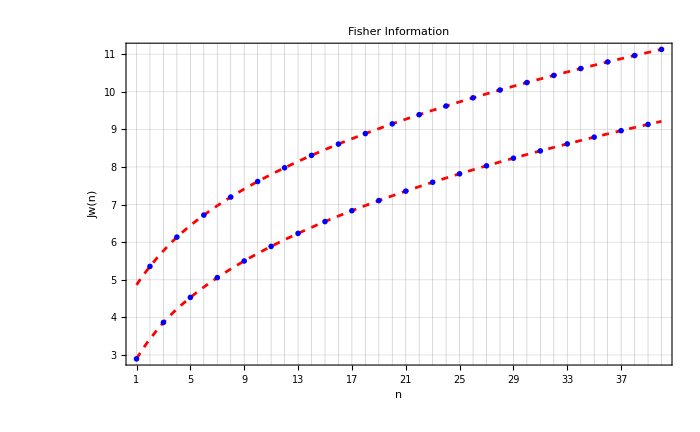

{2.8980068058,5.3553301321,3.8662810418,6.1351148542,4.5310089267,6.720089759,5.057014435,7.2001699512,5.5002135521,7.6128871799,5.8872828773,7.9779744985,6.2333086679,8.3072566856,6.5477621693,8.6084511909,6.8370291869,8.8869088327,7.1056451713,9.1465111553,7.3569618835,9.3901745957,7.5935352099,9.6201529675,7.8173642814,9.8382286114,8.0300459512,10.045838387,8.2328784863,10.24415967,8.4269334329,10.434170801,8.6131067973,10.616694667,8.7921563582,10.792430801,8.9647294271,10.961979494,9.1313838739,11.125860202}

```mathematica
(* ---------Setting Parameter--------- *)
nmax=40;              (* The number of n *)
precision=50;   (* Max Extra Precision *)
InitializationValue[Jw]=RandomInteger[0,nmax];
Initialize[Jw]; (* Fisher Information *)
(* ------Start------ *)
For[n=1,n<=nmax,n++,
(* ----------initialization---------- *)
InitializationValue[b]=RandomInteger[0,n];
Initialize[b];
(* 1. Find p(x) and pk *)
p = PolynomialQuotient[x(LaguerreL[n-1,1,x])^2,LaguerreL[n,x],x];
pk=CoefficientList[p,x];
(* 2. Find q(x) and qk *)
q=PolynomialMod[x(LaguerreL[n-1,1,x])^2,LaguerreL[n,x]];
qk=CoefficientList[q,x];
(* 3. Find roots of Ln(x) *)
xr=Solve[LaguerreL[n,x]==0,x];
xr=x/.xr;
(* 4. Find a *)
a=(-1)^n n!;
(* 5. Find bi *)
Table[b[[k]]=1/(∏_(i=1)^n If[i≠k,xr[[k]]-xr[[i]],1]),{k,1,n}];
(* 6. Find Ei(xi) *)
Ei=Integrate[ⅇ^(-x/2)/(x-xi),{x,0,Infinity},PrincipalValue->True,Assumptions->{xi>0}];
(* 7. Calculate term0 *)
term0=-8n+4;
(* 8. Calculate term1 *)
term1=4(-1)^n∑_(k=0)^(n-1) pk[[k+1]] 2^(k+1)k!;
(* 9. Calculate term2 *)
term2=4(-1)^n a∑_(i=1)^n b[[i]](q/.{x->xr[[i]]})(Ei/.{xi->xr[[i]]});
(* 10. Calculate term3 *)
term3=4(-1)^n a∑_(i=1)^n b[[i]]*∑_(k=1)^(n-1) qk[[k+1]]*∑_(m=0)^(k-1) (xr[[i]])^m 2^(k-m)(k-m-1)!;
(* 11. Calculate Jw *)
Jw[[n]]=Block[{$MaxExtraPrecision=precision},N[term0+term1+term2+term3,11]];
(* ------End------ *)
WriteString["stdout","Jw(",n,") = ",Jw[[n]]];
WriteString["stdout",If[Mod[n,5]≠0,"\t","\n"]];
];
(* ---------Output--------- *)
Jwodd=Jw[[1;;nmax;;2]];
Jweven=Jw[[2;;nmax;;2]];
Jwoddline=Interpolation[Table[{i,Jwodd[[Round[(i+1)/2]]]},{i,1,nmax,2}]];
Jwevenline=Interpolation[Flatten[{{{1,4.864285619}},Table[{i,Jweven[[Round[i/2]]]},{i,2,nmax,2}]},1]];
(* ------Plot------ *)
ticks=Table[x,{x,1,nmax}];
p1=Plot[Jwoddline[x],{x,1,nmax},PlotStyle->{Red,Dashed},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{2.5,Automatic}}];
p2=Plot[Jwevenline[x],{x,1,nmax},PlotStyle->{Red,Dashed},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{2.5,Automatic}}];
p3=ListPlot[Jw,PlotStyle->Blue,PlotMarkers->{"*",Scaled[0.05]},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{2.5,Automatic}}];
Show[p1,p2,p3,PlotRange->{{1,nmax},{2.5,Automatic}},PlotRangePadding->{None,0.5},Frame->True,FrameTicks->{{Automatic,None},{ticks,None}},FrameLabel->{"n","Jw(n)"},GridLines->{ticks,Automatic}, PlotLabel->"Fisher Information",ImageSize->700]
(* End *)
Jw
```

# Part VI Tr(Jw)≥Tr(V^-1)

Comment :
W(q,p) = (ⅇ^(-(q^2+p^2)))/π(-1)^n L_n[2 q^2+2 p^2]
∴ Let q = r Cos[θ], p = r Sin[θ], r^2=q^2+p^2
∴ W(r Cos[θ], r Sin[θ]) = (ⅇ^(-r^2))/π(-1)^n L_n[2 r^2]
∴ <q^2> = ∫_(-∞)^∞ ∫_(-∞)^∞ W(q, p)q^2 ⅆqⅆp 
	= ∫_0^(2π) ∫_0^∞ W(r Cos[θ],r Sin[θ])(r Cos[θ])^2 rⅆrⅆθ
	=∫_0^(2π) ∫_0^∞ (ⅇ^(-r^2))/π(-1)^n L_n[2 r^2](r Cos[θ])^2 rⅆrⅆθ
  <p^2> = ∫_(-∞)^∞ ∫_(-∞)^∞ W(q, p)p^2 ⅆqⅆp 
  	= ∫_0^(2π) ∫_0^∞ (ⅇ^(-r^2))/π(-1)^n L_n[2 r^2](r Sin[θ])^2 rⅆrⅆθ
  <qp> = ∫_(-∞)^∞ ∫_(-∞)^∞ W(q, p)p^2 ⅆqⅆp 
  	= ∫_0^(2π) ∫_0^∞ (ⅇ^(-r^2))/π(-1)^n L_n[2 r^2](r Cos[θ])(r Sin[θ])rⅆrⅆθ 
∴ V = (<q^2> | <qp>
<qp> | <p^2>)

V(1) = 1.3333333333		V(2) = 0.80000000000	V(3) = 0.57142857143	V(4) = 0.44444444444	V(5) = 0.36363636364
V(6) = 0.30769230769	V(7) = 0.26666666667	V(8) = 0.23529411765	V(9) = 0.21052631579	V(10) = 0.19047619048
V(11) = 0.17391304348	V(12) = 0.16000000000	V(13) = 0.14814814815	V(14) = 0.13793103448	V(15) = 0.12903225806
V(16) = 0.12121212121	V(17) = 0.11428571429	V(18) = 0.10810810811	V(19) = 0.10256410256	V(20) = 0.097560975610
V(21) = 0.093023255814	V(22) = 0.088888888889	V(23) = 0.085106382979	V(24) = 0.081632653061	V(25) = 0.078431372549
V(26) = 0.075471698113	V(27) = 0.072727272727	V(28) = 0.070175438596	V(29) = 0.067796610169	V(30) = 0.065573770492
V(31) = 0.063492063492	V(32) = 0.061538461538	V(33) = 0.059701492537	V(34) = 0.057971014493	V(35) = 0.056338028169
V(36) = 0.054794520548	V(37) = 0.053333333333	V(38) = 0.051948051948	V(39) = 0.050632911392	V(40) = 0.049382716049

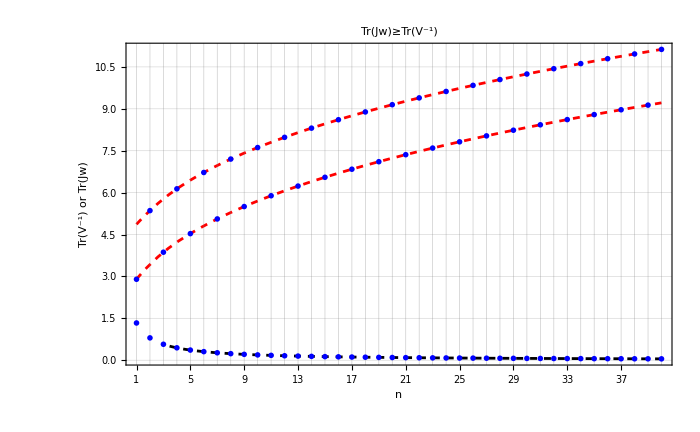

{1.3333333333,0.8,0.57142857143,0.44444444444,0.36363636364,0.30769230769,0.26666666667,0.23529411765,0.21052631579,0.19047619048,0.17391304348,0.16,0.14814814815,0.13793103448,0.12903225806,0.12121212121,0.11428571429,0.10810810811,0.10256410256,0.09756097561,0.093023255814,0.088888888889,0.085106382979,0.081632653061,0.078431372549,0.075471698113,0.072727272727,0.070175438596,0.067796610169,0.065573770492,0.063492063492,0.061538461538,0.059701492537,0.057971014493,0.056338028169,0.054794520548,0.053333333333,0.051948051948,0.050632911392,0.049382716049}

```mathematica
(* ---------Setting Parameter--------- *)
nmax=40;              (* The number of n *)
precision=50;   (* Max Extra Precision *)
InitializationValue[trv]=RandomInteger[0,nmax];
Initialize[trV]; (* Tr(V^-1) *)
(* ------Start------ *)
For[n=1,n<=nmax,n++,
Wnr=(ⅇ^(-r^2))/π(-1)^n LaguerreL[n,2 r^2];
(* <q^2> *)
Vq2=Integrate[Wnr(r Cos[θ])^2 r,{r,0,Infinity},{θ,0,2π}];
(* <p^2> *)
Vp2=Integrate[Wnr(r Sin[θ])^2 r,{r,0,Infinity},{θ,0,2π}];
(* <qp> *)
Vqp=Integrate[Wnr(r Cos[θ])(r Sin[θ])r,{r,0,Infinity},{θ,0,2π}];
(* V *)
V={{Vq2,Vqp},{Vqp,Vp2}};
(* Tr(V^-1) *)
trV[[n]]=Block[{$MaxExtraPrecision=precision},N[Tr[Inverse[V]],11]];
(* ------End------ *)
WriteString["stdout","V(",n,") = ",trV[[n]]];
WriteString["stdout",If[Mod[n,5]≠0,If[n==1,"\t\t","\t"],"\n"]];
];
(* ---------Output--------- *)
trVline=Interpolation[Table[{i,trV[[i]]},{i,1,nmax}]];
(* ------Plot------ *)
ticks=Table[x,{x,1,nmax}];

p1=Plot[Jwoddline[x],{x,1,nmax},PlotStyle->{Red,Dashed},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{0,Automatic}}];
p2=Plot[Jwevenline[x],{x,1,nmax},PlotStyle->{Red,Dashed},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{0,Automatic}}];
p3=Plot[trVline[x],{x,1,nmax},PlotStyle->{Black,Dashed},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{0,Automatic}}];
p4=ListPlot[Jw,PlotStyle->Blue,PlotMarkers->{"*",Scaled[0.05]},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{0,Automatic}}];
p5=ListPlot[trV,PlotStyle->Blue,PlotMarkers->{"*",Scaled[0.05]},Ticks->{ticks,Automatic},PlotRange->{{1,nmax},{0,Automatic}}];
Show[p1,p2,p3,p4,p5,PlotRange->{{1,nmax},{0,Automatic}},PlotRangePadding->{None,0.5},Frame->True,FrameTicks->{{Automatic,None},{ticks,None}},FrameLabel->{"n","Tr(V^-1) or Tr(Jw)"},GridLines->{ticks,Automatic}, PlotLabel->"Tr(Jw)≥Tr(V^-1)",ImageSize->700]
(* End *)
trV
```